```mathematica
Table[Length[FindFullFormula4[PathGraph[Range[k]]]],{k,1,10}]
```

{0,0,0,1,6,25,90,301,966,3025}

```mathematica
Table[Length[FindFullFormula[PathGraph[Range[k]]]],{k,1,11}]
```

{1,1,2,5,15,52,203,877,4140,21147,115975}

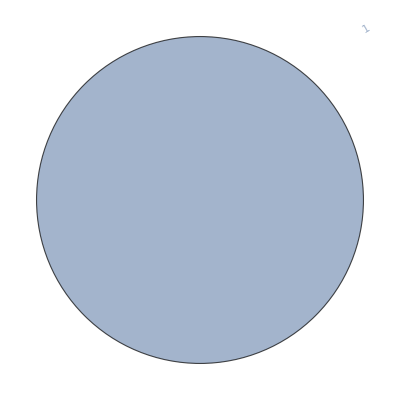
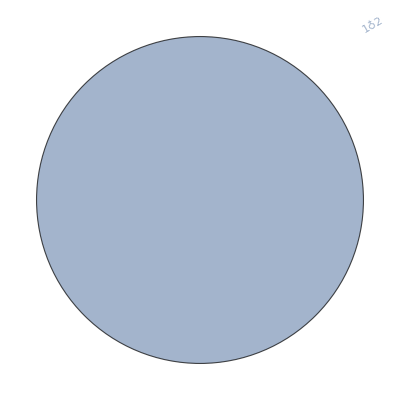
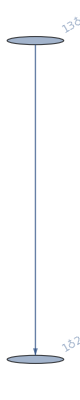
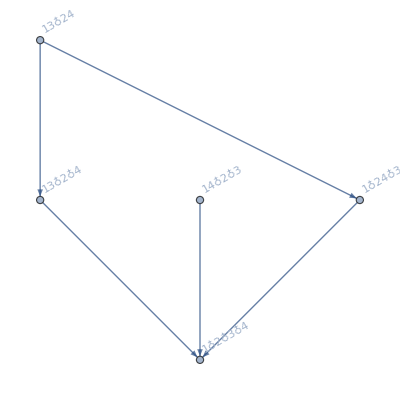
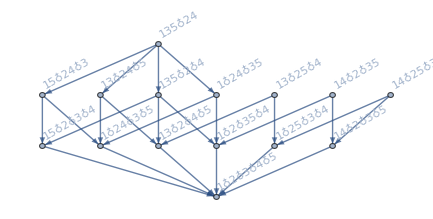

```mathematica
Table[FormulaGraphReverse[FindFullFormula[PathGraph[Range[k]]]],{k,1,5}]
```

```mathematica
Table[Length[FindFullFormula[MinimalGraph[k]]],{k,1,11}]
```

{1,1,1,2,5,15,52,203,877,4140,21147}

```mathematica
Table[Length[FindFullFormula4[MinimalGraph[k]]],{k,1,11}]
```

{0,0,1,1,1,1,1,1,1,1,1}

```mathematica
Table[Length[FindFullFormula4[JacobsThalGraph[k]]],{k,1,7}]
```

{1,3,5,11,21,43,85}

```mathematica
Table[Length[FindFullFormula[JacobsThalGraph[k]]]/2,{k,1,7}]
```

{1,4,11,41,162,715,3425}




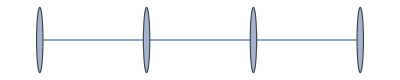
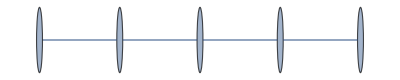
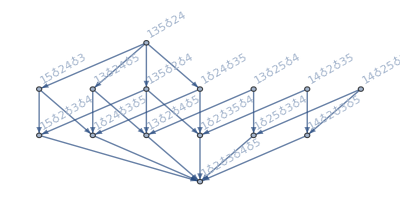
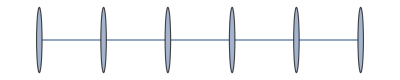
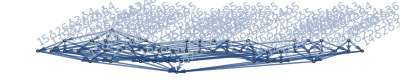
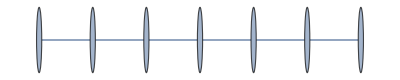
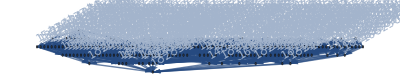
{-Graphics-→-Graphics-1,-Graphics-→-Graphics-2,-Graphics-→-Graphics-3,-Graphics-→-Graphics-4,-Graphics-→-Graphics-5,-Graphics-→-Graphics-6,-Graphics-→-Graphics-7}

```mathematica
Table[With[{g=PathGraph[Range[k]]},g->Labeled[FormulaGraphReverse[FindFullFormula[g]],Style[VertexCount[g],Red]]],{k,1,7}]
```

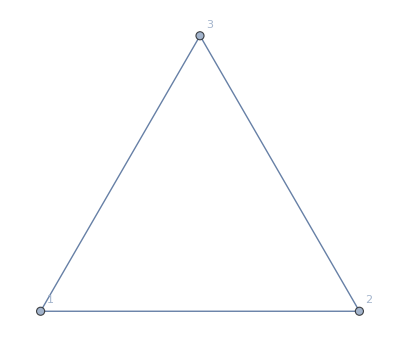
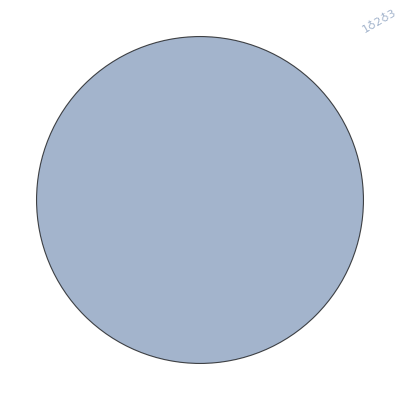
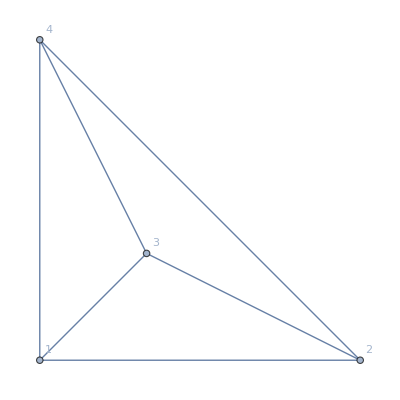
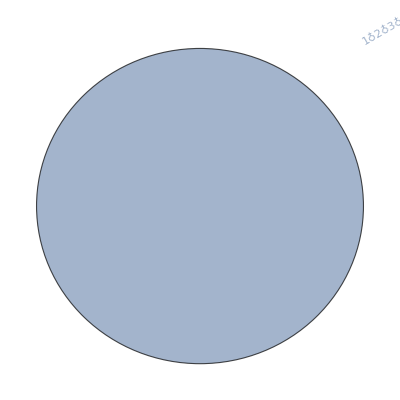
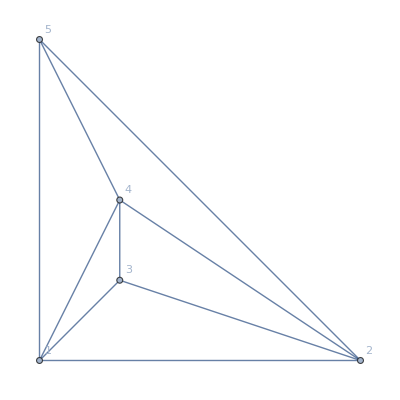
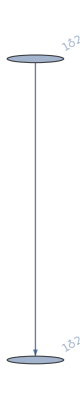
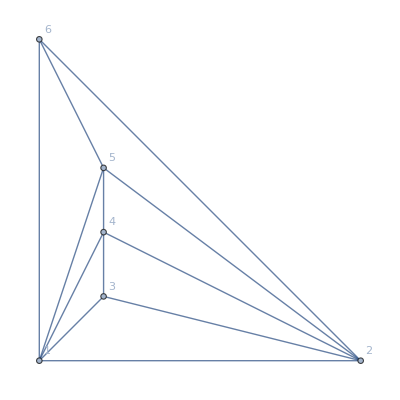
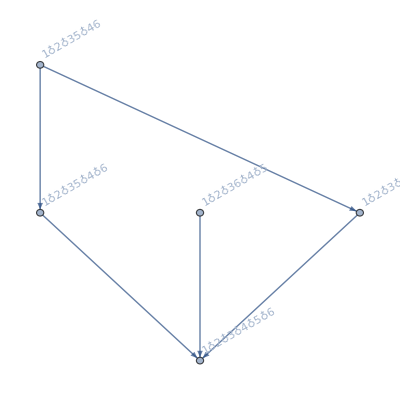
{-Graphics-→-Graphics-3,-Graphics-→-Graphics-3,-Graphics-→-Graphics-4,-Graphics-→-Graphics-5,-Graphics-→-Graphics-6,-Graphics-→-Graphics-7,-Graphics-→-Graphics-8}

```mathematica
Table[With[{g=MinimalGraph[k]},g->Labeled[Graph[FormulaGraphReverse[FindFullFormula[g]]],Style[VertexCount[g],Red]]],{k,1,7}]
```

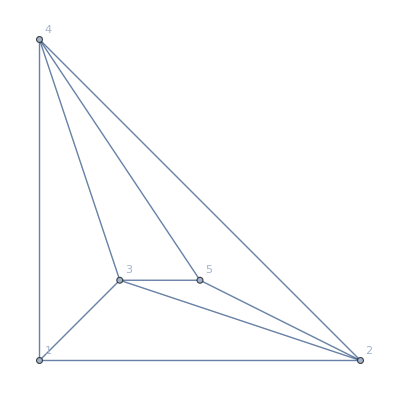
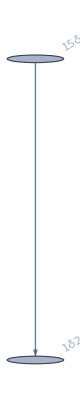
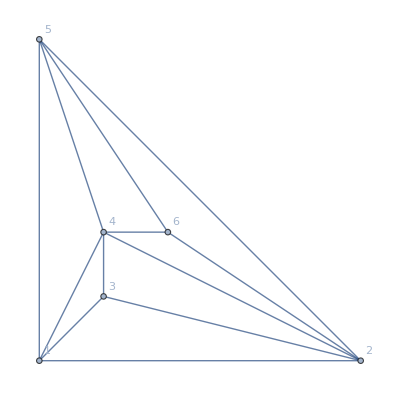
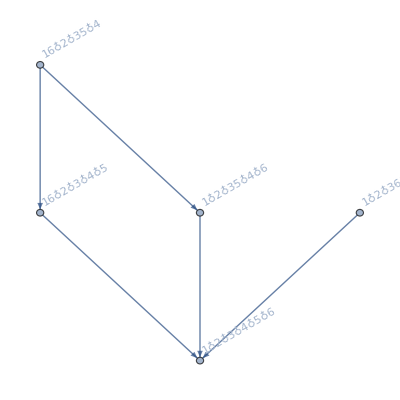
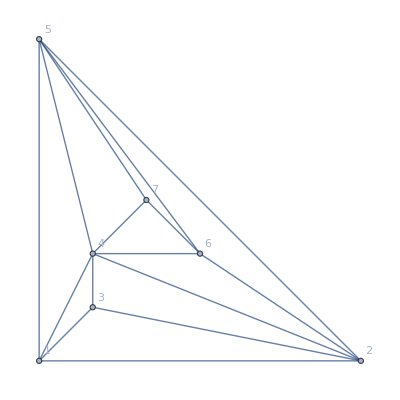
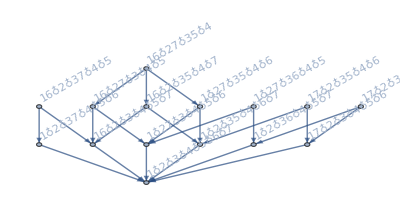
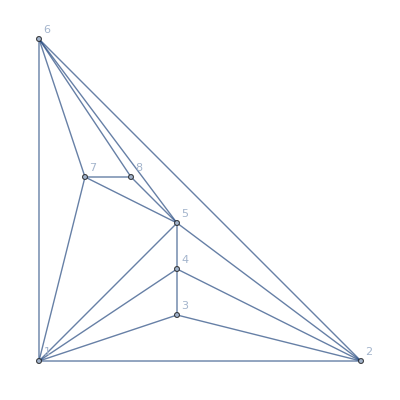
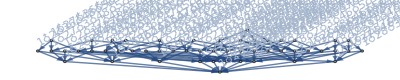
{-Graphics-→-Graphics-3,-Graphics-→-Graphics-3,-Graphics-→-Graphics-4,-Graphics-→-Graphics-5,-Graphics-→-Graphics-6,-Graphics-→-Graphics-7,-Graphics-→-Graphics-8}

```mathematica
Table[With[{g=MinimalGraph2[k]},g->Labeled[Graph[FormulaGraphReverse[FindFullFormula[g]]],Style[VertexCount[g],Red]]],{k,1,7}]
```

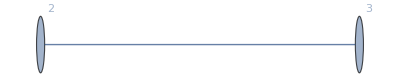
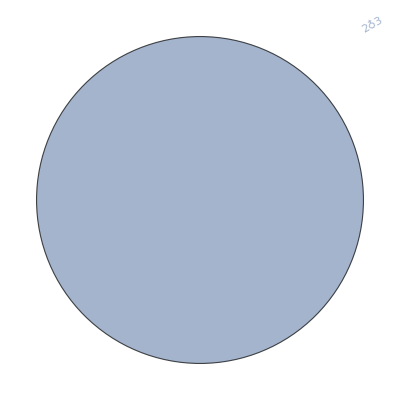
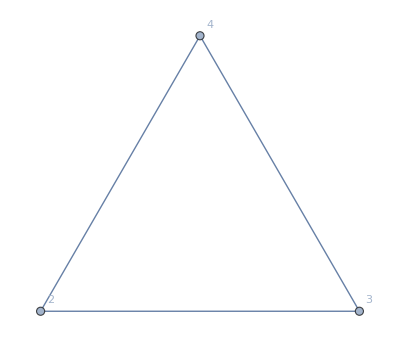
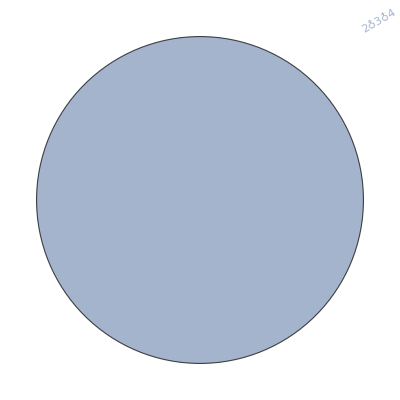
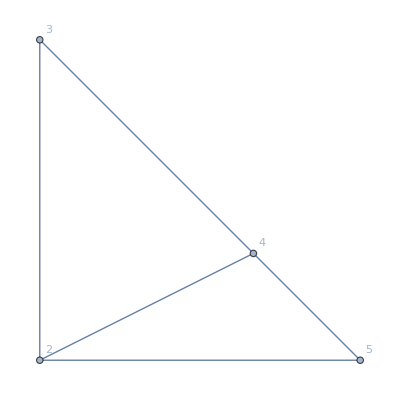
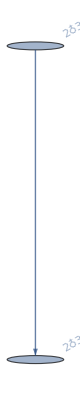
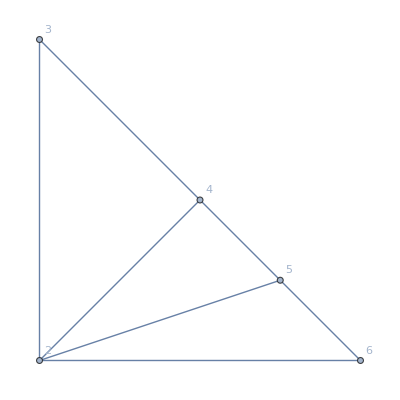
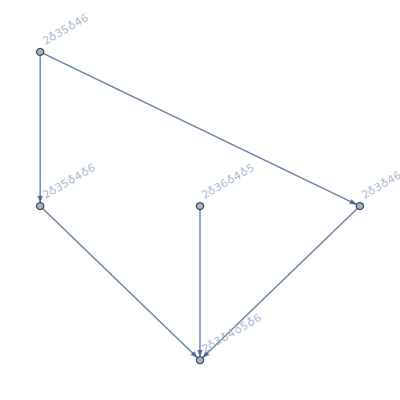
{-Graphics-→-Graphics-2,-Graphics-→-Graphics-2,-Graphics-→-Graphics-3,-Graphics-→-Graphics-4,-Graphics-→-Graphics-5,-Graphics-→-Graphics-6,-Graphics-→-Graphics-7}

```mathematica
Table[With[{g=VertexDelete[MinimalGraph[k],1]},g->Labeled[Graph[FormulaGraphReverse[FindFullFormula[g]]],Style[VertexCount[g],Red]]],{k,1,7}]
```

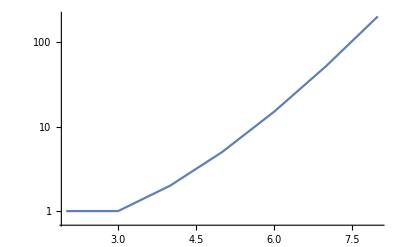

```mathematica
ListLogPlot[Table[With[{g=VertexDelete[MinimalGraph[k],1]},{VertexCount[g],Length[FindFullFormula[g]]}],{k,1,8}],Joined->True]
```

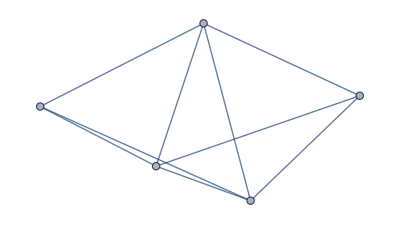
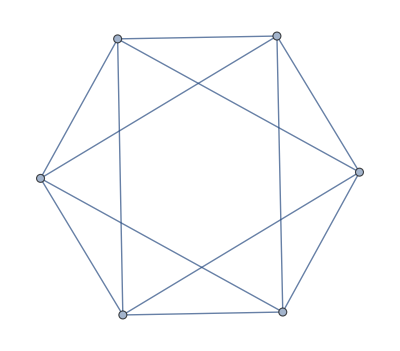
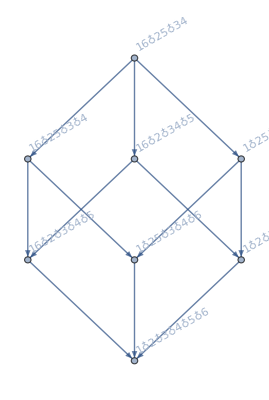
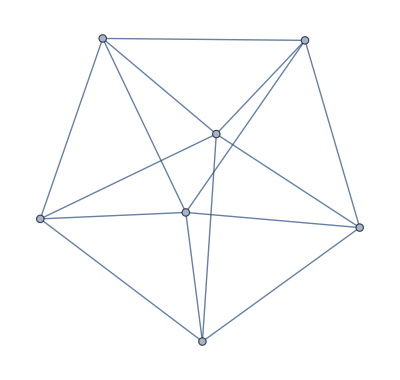
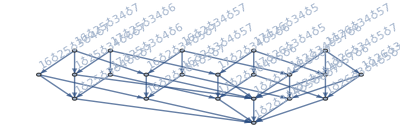
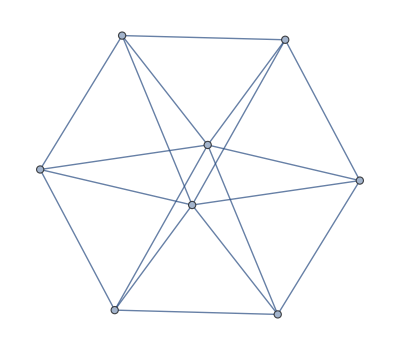
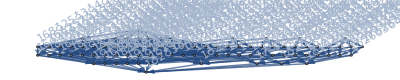
{-Graphics-→-Graphics-5,-Graphics-→-Graphics-6,-Graphics-→-Graphics-7,-Graphics-→-Graphics-8}

```mathematica
Table[With[{g=JacobsThalGraph[k]},g->Labeled[FormulaGraphReverse[FindFullFormula[g]],Style[VertexCount[g],Red]]],{k,1,4}]
```

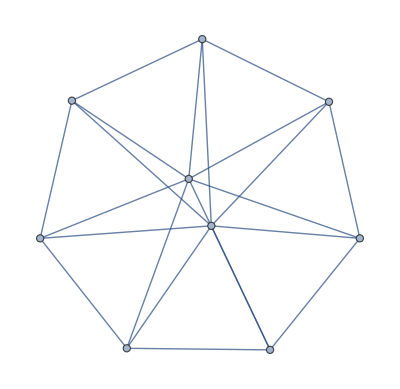
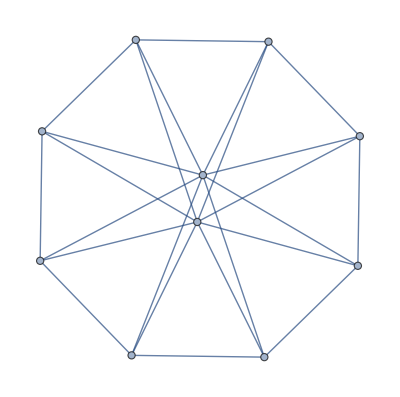
{-Graphics-→{{4,1},{5,1}}{5,1},-Graphics-→{{3,1},{4,3},{5,3},{6,1}}{6,4},-Graphics-→{{4,5},{5,10},{6,6},{7,1}}{7,11},-Graphics-→{{3,1},{4,11},{5,30},{6,29},{7,10},{8,1}}{8,41},-Graphics-→{{4,21},{5,91},{6,126},{7,70},{8,15},{9,1}}{9,162},-Graphics-→{{3,1},{4,43},{5,273},{6,525},{7,420},{8,146},{9,21},{10,1}}{10,715}}

```mathematica
Table[With[{g=JacobsThalGraph[k]},g->With[{form=FindFullFormula[g]},Labeled[Map[SymbolLevel,form]//Tally//Sort,Style[{VertexCount[g],Length[form]/2},Red]]]],{k,1,6}]
```

```mathematica
MinimalGraph[3]
```

-Graphics-